```mathematica
Clear["Global*`"];
SetDirectory[NotebookDirectory[]]
```

/Users/exec.142857/Downloads/Max_Lucas_task_8

## Bézier module, metamorph equivalent on Mathematica

The Fantômas team (2021)
21/07/14: Ryan’s first draft
21/07/15: Max adds file input and output
21/07/15: Aurore  sketches the final structure
21/08/05: Merged Max and Ryan with Read and Write
21/08/12: Max modified for task 8.

```mathematica
FlavorLabels={"\!\(\*OverscriptBox[\(b\), \(-\)]\)","\!\(\*OverscriptBox[\(c\), \(-\)]\)","\!\(\*OverscriptBox[\(s\), \(-\)]\)","\!\(\*OverscriptBox[\(u\), \(-\)]\)","\!\(\*OverscriptBox[\(d\), \(-\)]\)","g","d","u","s","c","b"};
```

Default carrier function

```mathematica
Fc[x_,{α0_,α1_,α2_}]:=α0*x^α1(1-x)^α2
```

## Metamorph Module (CAUTION: THIS NOTEBOOK TAKES POINTS OF THE FORM: ( X, PDF(X) )

The Reading Module
ReadOptions module creates the required arrays containing parameters needed throughout the bezier module by importing a .card file with proper formatting. 
The read parameters are the following:
- Carrier function parameters: coefficient a_0 and powers  a_1,  a_2
- Mapping mode: choose between direct input of Y-coordinates or one of two softsign function mapping modes by which the Y-coordinates are computed
-xPower: the chosen power assigned to x which together constitute the argument of Bézier polynomials
- x: X-coordinates of control points
- Sm: Y-coordinates/parameters associated to the softsign function
- fp and fm: Upper and lower boundaries for each Y-coordinate

```mathematica
ReadOptions[filename_]:=Module[{i,f,sl,fpl,fml,nmin,Imp,val},
read=OpenRead[filename];
Skip[read,Record,1];
name=Read[read ,String];
nameb=StringSplit[name,","];
a12s=Read[read,{Number, Number,Number,String}];
as={a12s[[1]],a12s[[2]],a12s[[3]]};
ppow=Read[read, {Number, Number,String}];
mappingmode=ppow[[1]];
xPower=ppow[[2]];
Read[read,{String}];
nmin=Length@Import[read,"Lines"];
Imp=Import[read,"Table"];
xlist=List[];
slist=List[];
fplist=List[];
fmlist=List[];
pdflist=List[];
ptsmin=List[];
ptsplus=List[];
For[i=1,i≤nmin,i++,AppendTo[xlist,Imp[[i,1]]];AppendTo[slist,Imp[[i,2]]];AppendTo[fplist,Imp[[i,4]]];AppendTo[fmlist,Imp[[i,5]]]];
Which[mappingmode==0,pdflist=slist,mappingmode==1,f[sl_,fpl_,fml_]:=(fpl+fml)/2+(fpl-fml)*sl/2,mappingmode==2,f[sl_,fpl_,fml_]:=(fpl+fml)/2+(fpl-fml)*sl/(2*(1+Abs[sl]))];
Which[mappingmode==0,Null,mappingmode==1,For[i=1,i≤nmin,i++,AppendTo[pdflist,f[slist[[i]],fplist[[i]],fmlist[[i]]]]],mappingmode==2,For[i=1,i≤nmin,i++,AppendTo[pdflist,f[slist[[i]],fplist[[i]],fmlist[[i]]]]]];
ptsmin=Transpose[{xlist,fmlist}];
ptsplus=Transpose[{xlist,fplist}];
Close[read];
Return["Parameter lists created."]
]
```

The Bézier Module
The Bezier module computes and returns the C_l coefficients, employing the parameters acquired from the ReadOptions module. 
The input parameters are:
-a012: list of carrier function parameters. The default list is as, which was created inside the ReadOptions module.
-xPow: x’s scaling power. Its default value is xPower, read from the .card file in the ReadOptions module.
- k: number of points to be considered for the fit (FOR CODE REASONS, IT SHOULD COINCIDE WITH n)
-n: degree of the fit polynomial
-nMellin: Mellin moments, not implemented yet

```mathematica
Bezier[a012_:as,xPow_:xPower,k_:1,n_:1,nMellin_:1]:= Module[{m,nlist,M,t,T,p,l,x,P,C,f,b,B,pts,plotmod,errplotmod},
Params=List[];
AppendTo[Params,a012];
AppendTo[Params,xPow];
AppendTo[Params,k];
AppendTo[Params,n];
AppendTo[Params,nMellin];
nlist=Range[0,n];
m[p_,l_]:=(-1)^(p-l)Binomial[n,l]Binomial[n-l,n-p];
M=Array[m,{n+1,n+1},{{0,n},{0,n}}];
t[x_,p_]:=x^(p*xPow);
T=ArrayReshape[Table[Rationalize[t[x,p],0],{x,xlist},{p,nlist}],{k+1,n+1}];
P=ArrayReshape[pdflist/Fc[xlist,a012],{k+1,1}];
C=Inverse[M].Inverse[Rationalize[Transpose[T].T,0]].Transpose[T].P;
Coef=C;
Return[C];
]
```

The Output Module
The BezierOutput module returns the plot of the Bézier fit and the explicit expression of the polynomial. Additionally, the module creates an output .card file with the same formatting as the input files. The module requires only one parameter:
-list: a list containing the parameters needed for the fit. Its default value is Params, which is the list of parameters created in the Bezier module.

```mathematica
BezierOutput[list_:Params]:=Module[{a012,xPower,k,n,plotmod,pdfplot,l,b,pts,f,B,nMellin,Cl,Tl,fil},
{a012,xPower,k,n,nMellin}={Params[[1]],Params[[2]],Params[[3]],Params[[4]],Params[[5]]};
b[l_]:=Binomial[n,l](x^xPower)^l(1-x^xPower)^(n-l);
B=ArrayReshape[Array[b,n+1,{0,n}],{1,n+1}];
f:=B.Coef;
pts=Transpose[{xlist,pdflist/Fc[xlist,a012]}];
plotmod=Show[Plot[{f(*,pdffunc*)},{x,10^(-5),.99},
PlotStyle->{Blue,Darker[Green]},
 PlotLabel->Style["Modulator Bézier Fit of "<>nameb[[1]]<>" from"<>nameb[[2]],FontSize->14],
 PlotLegends->{"Computed Bézier Curve","Analytic Modulator Function"},
PlotRange->{-0.5,7}], ListPlot[pts,PlotStyle->{PointSize[Large],Red},PlotLegends->{"Control Points"}],ImageSize->Large,AxesLabel->{"x","f(x)"},LabelStyle->Directive[Bold]];
pdfplot=Plot[f*Fc[x,a012],{x,0,1.2},PlotStyle->Red,
PlotRange->{-0.5,2.5},ImageSize->Large,AspectRatio->1/2,
PlotLabel->nameb[[1]]<>" x*PDF plot"];
CellPrint@ExpressionCell[#,"Output"]&/@{plotmod,pdfplot};
Cl=List[];
For[i=1,i≤n+1,i++,AppendTo[Cl,Coef[[i,1]]]];
Coefs=Cl;
fil=OpenWrite["test.card",PageWidth->Infinity];
Write[fil,OutputForm["# Fantômas4QCD, from Mathematica, "], OutputForm[DateString[Today,"ISODate"]]];
Write[fil,OutputForm[nameb[[1]]],OutputForm[","],OutputForm[nameb[[2]]]];
Write[fil,OutputForm[Params[[1,1]]],OutputForm["\t"],OutputForm[Params[[1,2]]],OutputForm["\t"],OutputForm[Params[[1,3]]],OutputForm["\t:"],OutputForm["a0\ta1\ta2"]];
Write[fil,OutputForm[mappingmode],OutputForm["\t"],OutputForm[xPower],OutputForm["\t\t"],OutputForm[":Mapping Mode\t"],OutputForm["xPower"]];
Write[fil,OutputForm["# x\tSm\tC\tfp\tfm"]];
For[i=1,i≤n+1,i++,Write[fil,CForm[xlist[[i]]],OutputForm["\t"],CForm[slist[[i]]],OutputForm["\t"],CForm[Cl[[i]]],OutputForm["\t"],CForm[fplist[[i]]],OutputForm["\t"],CForm[fmlist[[i]]]]];
Close[fil];
Return[f[[1,1]]]
]
```

## EXAMPLES

### uV

Use createlist for preexisting functions ....implement

Parameter lists created.

Up Valence

CT18NNLO

{{2.13375},{-0.14722},{2.56498},{1.38161},{1.}}

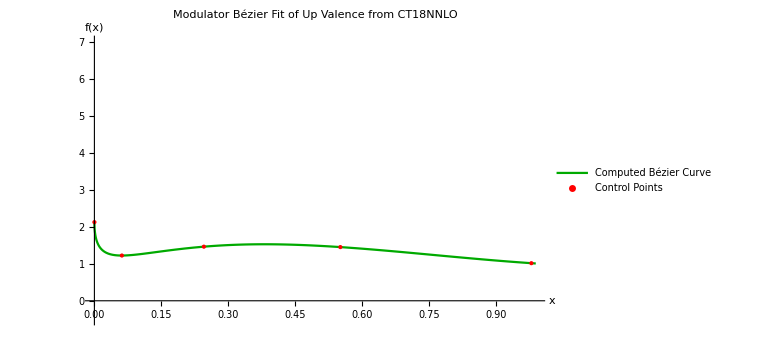

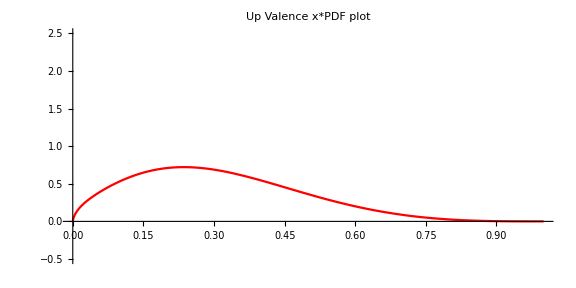

2.13375 (1-x^0.5)^4-0.588878 (1-x^0.5)^3 x^0.5+15.3899 (1-x^0.5)^2 x^1.+5.52643 (1-x^0.5) x^1.5+1. x^2.

```mathematica
(*Add 0 and 1 to the examples*)
ReadOptions["thes_test_uV.card"]
nameb[[1]]="Up Valence"
nameb[[2]]=" CT18NNLO"
Bezier[as,0.5,4,4,1.3]
BezierOutput[Params]
```

```mathematica
Gluon
```

Gluon

Parameter lists created.

Gluon

CT18NNLO

{{10.3452},{2.54213},{-0.1551},{0.114433},{1.2124},{0.999999}}

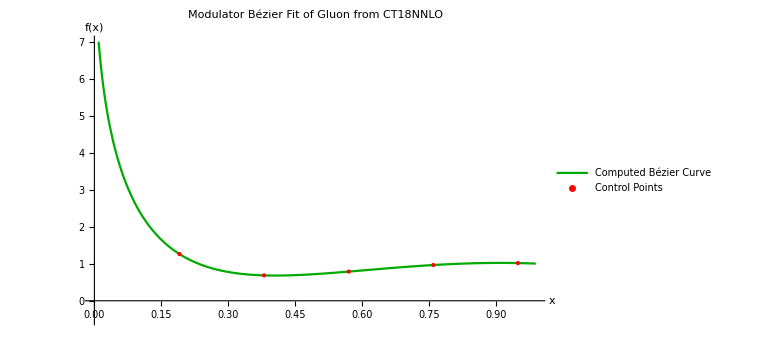

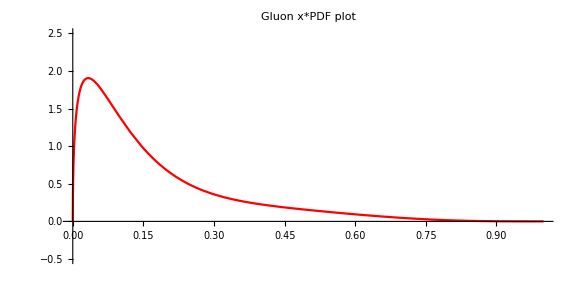

10.3452 (1-√x)^5+12.7106 (1-√x)^4 √x-1.551 (1-√x)^3 x+1.14433 (1-√x)^2 x^(3/2)+6.06201 (1-√x) x^2+0.999999 x^(5/2)

```mathematica
ReadOptions["thes_dup_test_gluon.card"]
nameb[[1]]="Gluon"
nameb[[2]]=" CT18NNLO"
Bezier[as,1/2,5,5,1.3]
BezierOutput[Params]
```

### dV

Parameter lists created.

Down-Valence

CT18NNLO

{{6.79896},{6.40139},{4.09674},{4.66944},{6.89902},{1.39669},{0.999158}}

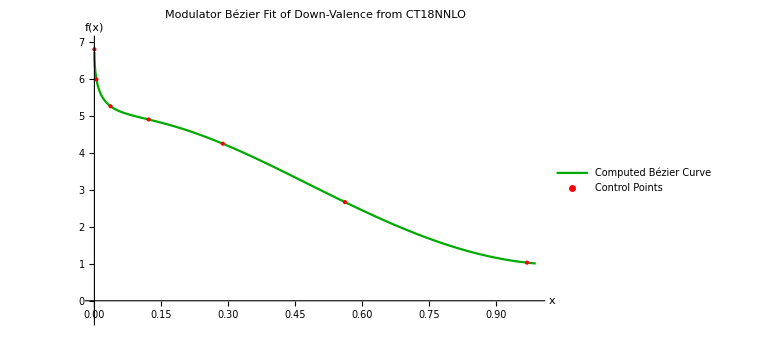

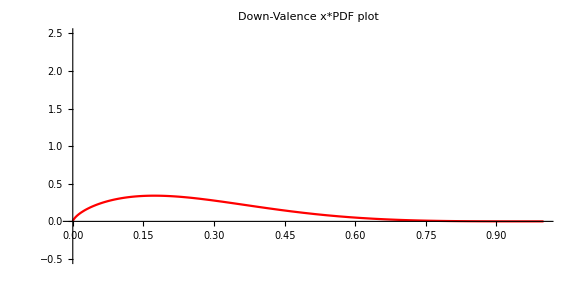

6.79896 (1-x^(1/3))^6+38.4083 (1-x^(1/3))^5 x^(1/3)+61.4511 (1-x^(1/3))^4 x^(2/3)+93.3888 (1-x^(1/3))^3 x+103.485 (1-x^(1/3))^2 x^(4/3)+8.38013 (1-x^(1/3)) x^(5/3)+0.999158 x^2

```mathematica
ReadOptions["thes_test_dv.card"]
nameb[[1]]="Down-Valence"
nameb[[2]]=" CT18NNLO"
Bezier[as,1/3,6,6,1.3]
BezierOutput[Params]
```

### Strange

Parameter lists created.

Strange

CT18NNLO

{{1.},{0.951407},{-0.218618},{1.39677},{-1.233},{1.25446},{0.629215},{1.10023},{0.970919},{1.00606},{0.99951}}

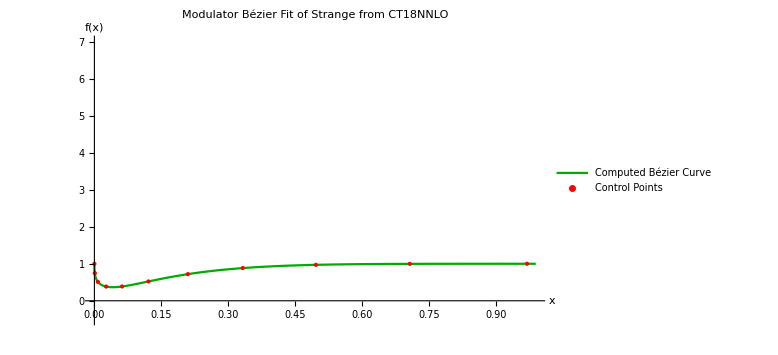

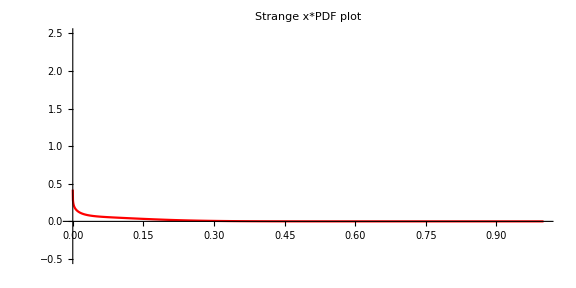

1. (1-x^(1/3))^10+9.51407 (1-x^(1/3))^9 x^(1/3)-9.83779 (1-x^(1/3))^8 x^(2/3)+167.613 (1-x^(1/3))^7 x-258.93 (1-x^(1/3))^6 x^(4/3)+316.125 (1-x^(1/3))^5 x^(5/3)+132.135 (1-x^(1/3))^4 x^2+132.028 (1-x^(1/3))^3 x^(7/3)+43.6914 (1-x^(1/3))^2 x^(8/3)+10.0606 (1-x^(1/3)) x^3+0.99951 x^(10/3)

```mathematica
ReadOptions["thes_test_s.card"]
nameb[[1]]="Strange"
nameb[[2]]=" CT18NNLO"
Bezier[as,1/3,10,10,1.3]
BezierOutput[Params]
```

### uV Transversity F_c(x)=x^0.25

```mathematica
ReadOptions["h1_uV_x_s_fp_fm_ep.card"]
xlist
slist
fplist
fmlist
pdflist
```

Parameter lists created.

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{9.07167×10^-6,-0.169901,-0.00709091,0.104698,0.0335942,0.0720823,0.146945,0.116469,0.463981,1.0998,-191.126}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.00001,-0.0877778,-0.00419812,0.0569433,0.0200369,0.04326,0.0856759,0.0708764,0.210485,0.280144,-0.000098959}

{{-778.608},{2232.6},{-4915.76},{9163.78},{-14945.5},{21556.6},{-27434.4},{30306.},{-27785.9},{18384.1},{-2563.39}}

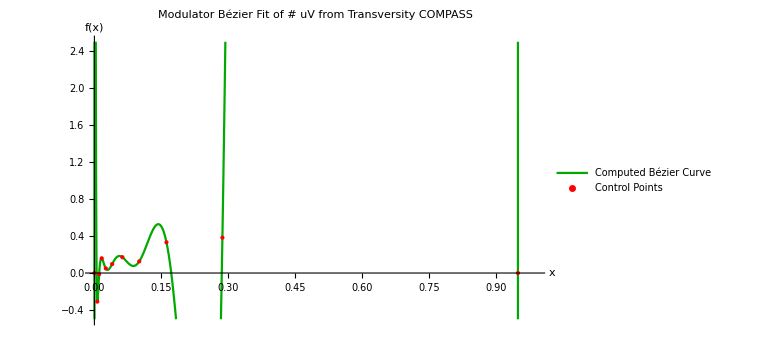

-778.608 (1-x^0.3)^10+22326. (1-x^0.3)^9 x^0.3-221209. (1-x^0.3)^8 x^0.6+1.09965×10^6 (1-x^0.3)^7 x^0.9-3.13855×10^6 (1-x^0.3)^6 x^1.2+5.43226×10^6 (1-x^0.3)^5 x^1.5-5.76121×10^6 (1-x^0.3)^4 x^1.8+3.63672×10^6 (1-x^0.3)^3 x^2.1-1.25037×10^6 (1-x^0.3)^2 x^2.4+183841. (1-x^0.3) x^2.7-2563.39 x^3.

```mathematica
Bezier[as,0.3,10,10,1.3]
BezierOutput[Params]
```

```mathematica
Coefs
```

{-778.608,2232.6,-4915.76,9163.78,-14945.5,21556.6,-27434.4,30306.,-27785.9,18384.1,-2563.39}

### uV Transversity F_c(x)=x^0.25,updated s values

```mathematica
ReadOptions["MOD_h1_uV_x_s_fp_fm_ep.card"]
xlist
slist
fplist
fmlist
pdflist
```

Parameter lists created.

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

{{-7631.25},{21674.},{-46914.2},{86247.1},{-139448.},{200498.},{-255776.},{284570.},{-263621.},{176348.},{-24617.9}}

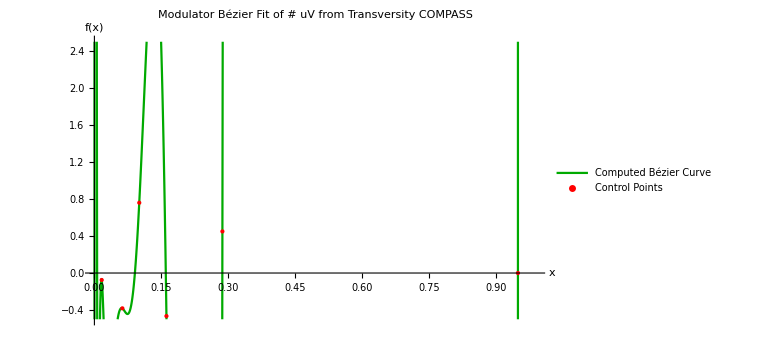

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Bezier[as,0.3,10,10,1.3]
BezierOutput[Params]
```

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}

### uV Transversity F_c(x)=x^0.25(less points)

Set::write: Tag Times in Transversity uV x F_c is Protected.

less points x^0.25

```mathematica
createlists["Cop_h1_uV_x_s_fp_fm_ep.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[Cop_h1_uV_x_s_fp_fm_ep.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
bezier[6,0.3,7,7, 1.3]
BezierOutput[Params]
```

bezier[6,0.3,7,7,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}

### uV Transversity F_c(x)=x^0.25(odd points)

Set::write: Tag Times in Transversity uV x F_c is Protected.

odd points x^0.25

```mathematica
createlists["uVodd_output1.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[uVodd_output1.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
bezier[6,0.3,5,5,1.3]
BezierOutput[Params]
```

bezier[6,0.3,5,5,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}

### uV Transversity F_c(x)=x^0.5(1-x)^3(less points)

```mathematica
createlists["Cop2_h1_uV_x_s_fp_fm_ep.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[Cop2_h1_uV_x_s_fp_fm_ep.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
h1uV={1,0.5,3}
aFc={ag,auV,as,aub,adb,h1uV};
bezier[6,0.5,7,7, 1.3]
BezierOutput[Params]
```

{1,0.5,3}

bezier[6,0.5,7,7,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

### dV Transversity F_c(x)=x^0.25

```mathematica
createlists["h1_dV_x_s_fp_fm_ep.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[h1_dV_x_s_fp_fm_ep.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
bezier[7,0.3,10,10,1.3]
BezierOutput[Params]
```

bezier[7,0.3,10,10,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}

### dV Transversity F_c(x)=x^0.25 ,updated s values

```mathematica
createlists["MOD_h1_dV_x_s_fp_fm_ep.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[MOD_h1_dV_x_s_fp_fm_ep.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
bezier[7,0.3,10,10,1.3]
BezierOutput[Params]
```

bezier[7,0.3,10,10,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}

### dV Transversity F_c(x)=x^0.25(odd points)

```mathematica
createlists["ODD_dV.card",2]
xlist
slist
fplist
fmlist
pdflist
```

createlists[ODD_dV.card,2]

{0.0001,0.0065,0.0106,0.0164,0.0255,0.0398,0.0627,0.1006,0.1616,0.2871,0.95}

{2.1,-0.8,-1.7,-0.047,-2.4,-3.1,-0.4,1.7,-0.8,1.6,-8.6}

{1.10234,0.60442,0.59624,0.600822,0.616477,0.643408,0.668722,0.679419,0.664133,0.534866,0.0000994768}

{-1.10234,-0.60442,-0.59624,-0.600822,-0.616477,-0.643408,-0.668722,-0.679419,-0.664133,-0.534866,-0.0000994768}

{0.746748,-0.268631,-0.37541,-0.026971,-0.43516,-0.486479,-0.191064,0.427782,-0.29517,0.329149,-0.0000891146}

```mathematica
bezier[7,0.3,5,5,1.3]
BezierOutput[Params]
```

bezier[7,0.3,5,5,1.3]

-Graphics-

-7631.25 (1-x^0.3)^10+216740. (1-x^0.3)^9 x^0.3-2.11114×10^6 (1-x^0.3)^8 x^0.6+1.03497×10^7 (1-x^0.3)^7 x^0.9-2.9284×10^7 (1-x^0.3)^6 x^1.2+5.05256×10^7 (1-x^0.3)^5 x^1.5-5.37129×10^7 (1-x^0.3)^4 x^1.8+3.41484×10^7 (1-x^0.3)^3 x^2.1-1.1863×10^7 (1-x^0.3)^2 x^2.4+1.76348×10^6 (1-x^0.3) x^2.7-24617.9 x^3.

```mathematica
Coefs
```

{-7631.25,21674.,-46914.2,86247.1,-139448.,200498.,-255776.,284570.,-263621.,176348.,-24617.9}